```mathematica
NS[]
```

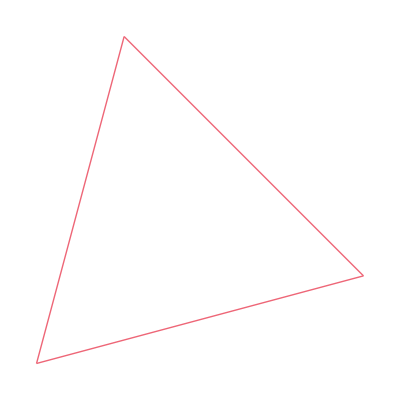

```mathematica
ClearAll[repr];n=2;
Co[x_]:=Flatten@{1-Total@Flatten@x,x};
u=Table[1,n+1];repr[f_]:=IdentityMatrix[{n,n+1}].RotationMatrix[{u,{0,0,1}}].f;
simp=Graphics[Sequence@@{red,Line[#]}&/@T/@(repr/@T/@Subsets[IdentityMatrix[n+1],{2}])]
```

```mathematica
freq[data_]:=(#/Total@#)&@(Count[data,#]&/@Range[3]);
```

```mathematica
ClearAll[f];MF/@(Evaluate[Array[f,3]]=Permutations[{6,1,1}/8])
```

{(3/4
1/8
1/8),(1/8
3/4
1/8),(1/8
1/8
3/4)}

```mathematica
f[4]=Table[1/3,3];
```

```mathematica
v=4;
```

```mathematica
likelihoodH[data_]:=Table[Times@@((f[m][[#]])&/@data),{m,v}]
```

```mathematica
posteriorH[data_]:=(#/Total@#)&@likelihoodH[data]
```

```mathematica
predictiveD[data_]:=T[Array[f,v]].posteriorH[data]
```

```mathematica
logscoreH[data_]:=Table[Mean[Table[Log[f[m][[data[[i]]]]],{i,1,t}]],{m,v}];
```

```mathematica
SeedRandom[666];ft=(#/Total@#)&@(1*f[1]+1*f[2]+1*f[3]+1*f[4]);data=RandomChoice[ft->Range[3],500];
```

```mathematica
{ft,(fe=freq[data])}//N
```

{{0.333333,0.333333,0.333333},{0.322,0.342,0.336}}

```mathematica
MF/@(seqposteriorH=Table[posteriorH[data[[;;t]]],{t,Length@data}])//N;
```

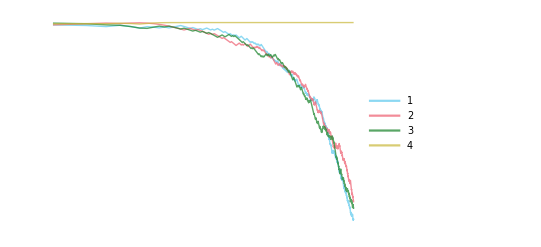

```mathematica
ListLogLogPlot[T@seqposteriorH,Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.75],solid}],PlotLegends->Placed[Range[v],{Left,Bottom}]]
```

```mathematica
MF/@(seqloglikelihoodH=Table[Log@likelihoodH[data[[;;t]]],{t,Length@data}])//N;
```

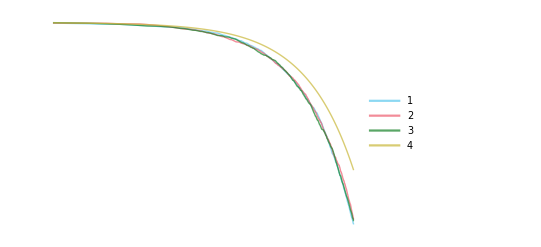

```mathematica
ListLogLinearPlot[T@seqloglikelihoodH,Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.75],solid}],PlotLegends->Placed[Range[v],{Left,Bottom}]]
```

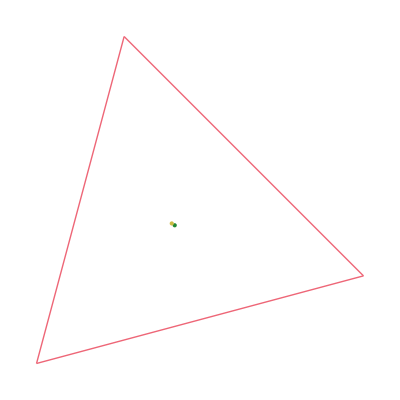

```mathematica
plseqposteriorH=ListPlot[repr/@seqposteriorH,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,plseqposteriorH,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
seqposteriorH[[2]]
```

{9/181,54/181,54/181,64/181}

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqposteriorH[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqposteriorH[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,50,1},AnimationRate->2]
```

```mathematica
MF/@(seqlogscoreH=Table[logscoreH[data[[;;t]]],{t,Length@data}])//N;
```

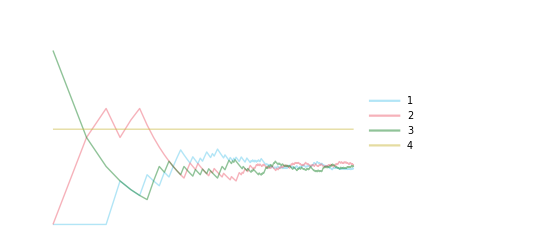

```mathematica
ListLogLinearPlot[T@seqlogscoreH,Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.5],solid}],PlotLegends->Placed[Range[v],{Center,Top}]]
```

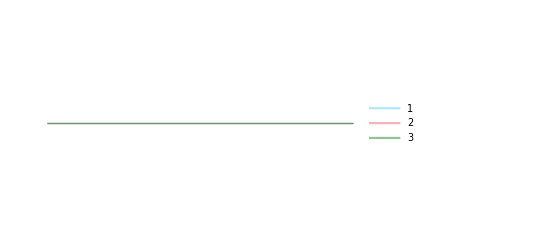

```mathematica
ListPlot[T@(seqlogscoreH-(seqloglikelihoodH/Range[Length@data])),Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.5],solid}],PlotLegends->Placed[Range[3],{Center,Top}]]
```

```mathematica
(MF/@(seqpredictiveD=Table[predictiveD[data[[;;t]]],{t,Length@data}]));
```

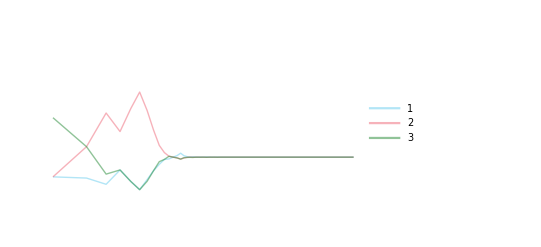

```mathematica
ListLogLinearPlot[T@seqpredictiveD,Joined->True,PlotRange->{All,{0,1}},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.5],solid}],PlotLegends->Placed[Range[v],{Center,Top}]]
```

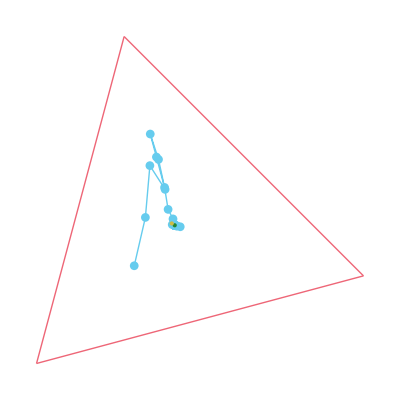

```mathematica
seqpredp=ListPlot[repr/@seqpredictiveD,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,seqpredp,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqpredictiveD[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqpredictiveD[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,20,1},AnimationRate->Auto]
```